```mathematica
Factor[x^2+2x+1==0]
```

(1+x)^2==0

```mathematica
Solve[x^2+5x-6==0, x]
```

{{x→-6},{x→1}}

```mathematica
Roots[x^2+5x-6==0, x]
```

x==-6||x==1

```mathematica
NSolve[7x^2+3x-5==0,x]
```

{{x→-1.08618},{x→0.657611}}

```mathematica
Solve[x^7+x^6+4*x^3-5x^2==0, x]
```

{{x→0},{x→0},{x→},{x→},{x→},{x→},{x→}}

```mathematica
NSolve[x^7+x^6+4*x^3-5x^2==0, x]
```

{{x→-1.48956-1.0058 ⅈ},{x→-1.48956+1.0058 ⅈ},{x→0.},{x→0.},{x→0.532169-1.18692 ⅈ},{x→0.532169+1.18692 ⅈ},{x→0.914781}}

```mathematica
Roots[x^7+x^6+4*x^3-5x^2==0, x]
```

x==0||x==0||x==||x==||x==||x==||x==



```mathematica
Graphics[Disk[]]
```

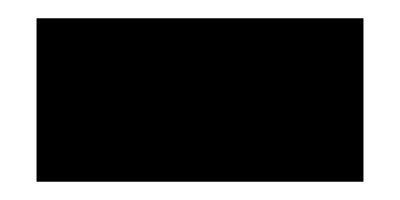

```mathematica
Graphics[Rectangle[{0,0}, {4,2}]]
```

```mathematica
Graphics[{Green, Rectangle[{0,0}, {4,2}], Red Disk[]}]
```

-Graphics-

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
rect = Rectangle[{0,0}, {4,2}]
```

Rectangle[{0,0},{4,2}]

```mathematica
Area[rect]
```

8

```mathematica
Volume[Cylinder[]]
```

```mathematica
2 π
```

```mathematica
exp = (Cos[x])^2/((Tan[x])^2-(Sin[x])^2)*(1/(Cos[x])^2-1)
```

(Cos[x]^2 (-1+Sec[x]^2))/(-Sin[x]^2+Tan[x]^2)

```mathematica
TrigFactor[exp]
```

Cot[x]^2

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
Solve[Cos[x]^2 + Sin[x]^2==x]
```

{{x→1}}

```mathematica
Print[Cos[x]^2 + Sin[x]^2==x]
```

Cos[x]^2+Sin[x]^2==x

```mathematica
Limit[(x^3-1)(x-1), x->1]
```

0

```mathematica
Limit[(x^3-1)(x-1), x->∞]
```

∞

```mathematica
Limit[1/x, x->0, Direction->1]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]
```

∞

```mathematica
D[x^6,x]
```

6 x^5

```mathematica
Sin'''''''''''''''''''''''''''''''''''''''''''''''''[x]
```

Cos[x]

```mathematica
f[x_]:=x^2+2x+1
```

```mathematica
f'[x]
```

2+2 x

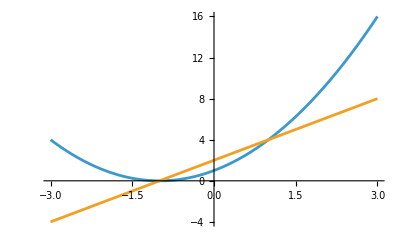

```mathematica
Plot[{f[x], f'[x]},{x,-3,3}]
```

```mathematica
D[x^6, {x,3}]
```

120 x^3

```mathematica
Sin''[x]
```

-Sin[x]

```mathematica
f[x_]=(Log[x])^(Tan[x])
```

Log[x]^Tan[x]

```mathematica
f'[x]
```

Log[x]^Tan[x] (Log[Log[x]] Sec[x]^2+Tan[x]/(x Log[x]))

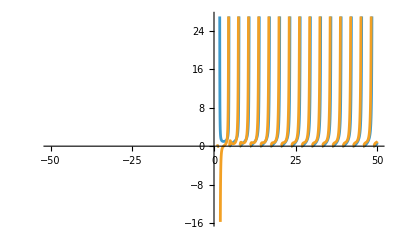

```mathematica
Plot[{f[x], f'[x]},{x,-50,50}]
```

```mathematica
Integrate[8x^4,x]
```

(8 x^5)/5

```mathematica
∫8x^4ⅆx
```

(8 x^5)/5

```mathematica
∫_0^4 8x^4ⅆx
```

8192/5

```mathematica
NIntegrate[x^3Sin[x]+2Log[3x]^2,{x,0,Pi}]
```

28.1531

```mathematica
D[Abs[x]^3, {x, 10}]
```

12600 (Abs^(3)[x])^2 Abs^(4)[x]+9450 Abs''[x] (Abs^(4)[x])^2+15120 Abs''[x] Abs^(3)[x] Abs^(5)[x]+7560 Abs'[x] Abs^(4)[x] Abs^(5)[x]+756 Abs[x] (Abs^(5)[x])^2+3780 Abs''[x]^2 Abs^(6)[x]+5040 Abs'[x] Abs^(3)[x] Abs^(6)[x]+1260 Abs[x] Abs^(4)[x] Abs^(6)[x]+2160 Abs'[x] Abs''[x] Abs^(7)[x]+720 Abs[x] Abs^(3)[x] Abs^(7)[x]+270 Abs'[x]^2 Abs^(8)[x]+270 Abs[x] Abs''[x] Abs^(8)[x]+60 Abs[x] Abs'[x] Abs^(9)[x]+3 Abs[x]^2 Abs^(10)[x]

```mathematica
Print[Abs[x]^3]
```

Abs[x]^3

```mathematica
NIntegrate[(Log[x])^(Tan[x]),{x,0,Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.57688}. NIntegrate obtained 7.30377327796633×10^7066+0.430294 ⅈ and 7.30377327796633×10^7066 for the integral and error estimates.

7.30377327796632×10^7066

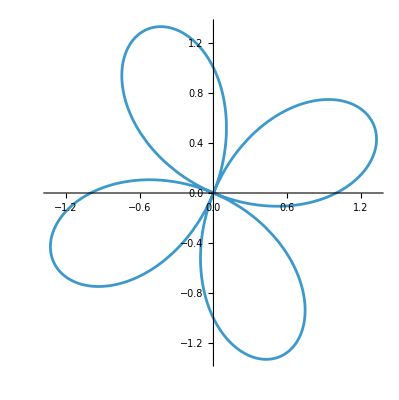

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ],{θ,0,2Pi}]
```

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

```mathematica
fab = Table[Fibonacci[x],{x,1,7}]
```

{1,1,2,3,5,8,13}

```mathematica
Total[fab]
```

33